```mathematica
FF[a_]:=Exp[a[[1]]]+Cos[a[[2]]]/a[[1]] Cos[Sin[a[[2]]]]
```

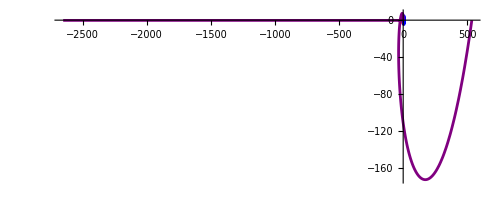

```mathematica
PolarPlot[{4 Sin[3 t],FF[{0.1,t}],FF[{t,2}]},{t,0,2 Pi},PlotStyle->{Red,Blue,Purple}]
```